Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

The following site: https://courses.washington.edu/ph227814/228/nb/Laurent.nb.pdf has info on Laurent series which looks pretty good. None of it was used in this section. Problems in this section do not deal per se with annular domains. Still, I’m sure they are useful for what they are.

```mathematica
Clear["Global`*"]
```

1 - 8 Laurent series near a singularity at 0
Expand the function in a Laurent series that converges for 0<|z|<R and determine the precise region of convergence.

1.  Cos[z]/z^4

```mathematica
Clear["Global`*"]
```

```mathematica
ff[z]=Cos[z]/z^4
```

Cos[z]/z^4

The series is created around 0, and according to the problem description, should be convergent around a certain z value and extending to the characteristic radius of the series. The Maclaurin series is created without difficulty, but it is understandable why the problem description specifically avoids assigning 0 to z. For this particular problem, purporting to deal with Laurent series, there seem to be no specific directions relative to the series creation by Mathematica. I suspect this is not a standard presentation of a Laurent series problem.

```mathematica
Series[ff[z],{z,0,8}]
```

1/z^4-1/(2 z^2)+1/24-z^2/720+z^4/40320-z^6/3628800+z^8/479001600+O[z]^9

The green cell above matches the answer in the text. I can go on to identify the radius of convergence, with a sequence of coefficients that looks very weird at first,

```mathematica
FindSequenceFunction[{1,-1/2,1/24,-1/720,1/40320,-1/3628800,1/479001600},n]
```

((-1)^(1+n) 4^(1-n))/(Pochhammer[1/2,-1+n] Pochhammer[1,-1+n])

```mathematica
FullSimplify[%]
```

(-1)^(1+n)/Gamma[-1+2 n]

The function for generating the sequence coefficients turns out to look pretty vanilla. The unusual character stemmed from the series exponents starting below zero and increasing through zero. Using Cauchy-Hadamard criterion,

```mathematica
Limit[Abs[(-1)^(1+n)/Gamma[-1+2 n](Gamma[-1+2( n+1)]/(-1)^(2+n))],n->∞]
```

∞

This is dissimilar to previous problems, for there is no n factor, hence no power term as used previously. I still feel a need to associate the exponent influence with a term number, so

```mathematica
FindSequenceFunction[{-4,-2,0,2,4,6,8},n]
```

2 (-3+n)

The above cell suggests that the effective exponent for the series is 2n. So to nail down the radius, I am going to do the following (though I don’t have evidence that it is correct in this situation)

```mathematica
∞^(1/2)
```

∞

The radius in the above cell must be influenced by the avoidance of 0 imposed by the problem description. Therefore I will express the radius of convergence as 0<|z|<∞, in agreement with the answer in the text.

As explained in example 1 on p. 712, the “annulus” of convergence for the Laurent series is the whole complex plane without the origin, and the principal part of the series at 0 is 1/z^4 -1/(2 z^2).

3.  Exp[z^2]/z^3

```mathematica
Clear["Global`*"]
```

```mathematica
fg[z_]=Exp[z^2]/z^3
```

(ⅇ^(z^2))/z^3

```mathematica
Series[fg[z],{z,0,8}]
```

1/z^3+1/z+z/2+z^3/6+z^5/24+z^7/120+O[z]^9

```mathematica
FindSequenceFunction[{1,1,1/2,1/6,1/24,1/120},n]
```

1/Pochhammer[1,-1+n]

```mathematica
FullSimplify[%]
```

1/Gamma[n]

```mathematica
Limit[Abs[1/Gamma[n](Gamma[( n+1)]/1)],n->∞]
```

∞

```mathematica
FindSequenceFunction[{-3,-1,1,3,5,7},n]
```

-5+2 n

```mathematica
∞^(1/2)
```

∞

The radius in the above cell must be influenced by the avoidance of 0 imposed by the problem description. Therefore I will express the radius of convergence as 0<|z|<∞, in agreement with the answer in the text.

As explained in example 1 on p. 712, the principal part of the series is 1/z^3+1/z.

5.  1/(z^2-z^3)

```mathematica
Clear["Global`*"]
```

The solution to this problem depends on examples 3 and 4 on p. 713. Example 3 explains that

1/(1-z)=∑_(n=0)^∞ z^n  is a valid statement if |z|<1 and
1/(1-z)=-1/(z(1-z^-1))=(-∑)_(n=0)^∞1/z^(n+1)=-1/z-1/z^2-...  is a valid statement if |z|>1

Example 4 deals with Laurent expansions in different concentric annuli and solves 1/(z^3-z^4) by piggy backing on example 3. In analogous fashion,

```mathematica
1/(z^2-z^3)==∑_(n=0)^∞ z^(n-2)==Sum[Sequence[z^(n-2)],{n,0,4}] (* for 0 < |z| < 1   Series#1*)
```

```mathematica
1/(z^2-z^3)==1/((1-z) z^2)==1+1/z^2+1/z+z+z^2
```

and

```mathematica
1/(z^2-z^3)==-∑_(n=0)^∞ 1/z^(n+3)==-Sum[Sequence[z^(-(n+3))],{n,0,4}] (* for |z| > 1  Series#2 *)
```

1/(z^2-z^3)==-1/((-1+z) z^2)==-1/z^7-1/z^6-1/z^5-1/z^4-1/z^3

Note although the text answer only covers the green cell above, the  yellow cell is also perfectly analogous to example 4 in the case where |z|>1.

In order to determine the inner radius of convergence, I suppose I will have to solve Series#1 using C-H.

```mathematica
FindSequenceFunction[{1,1,1,1,1},n]
```

1

The radius of convergence can be easily seen to be 1.

What about Series#2 using C-H?

```mathematica
FindSequenceFunction[{-1,-1,-1,-1,-1},n]
```

-1

```mathematica
Limit[Abs[-1/-1],n->∞]
```

1

The radius of convergence cannot extend past 1.  0 < |z| < 1 is what it has to be equal to.

This explains why the text answer does not include the yellow cell above.

7.  z^3 Cosh[1/z]

```mathematica
Clear["Global`*"]
```

```mathematica
fj[z_]=z^3 Cosh[1/z]
```

z^3 Cosh[1/z]

```mathematica
Series[fj[z],{z,∞,8}]
```

z^3+z/2+1/(24 z)+1/(720 z^3)+1/(40320 z^5)+1/(3628800 z^7)+O[1/z]^9

The above green cell matches the answer in the text.

```mathematica
FindSequenceFunction[{1,1/2,1/24,1/720,1/40320,1/3628800},n]
```

4^(1-n)/(Pochhammer[1/2,-1+n] Pochhammer[1,-1+n])

```mathematica
FullSimplify[%]
```

1/Gamma[-1+2 n]

```mathematica
Limit[Abs[1/Gamma[-1+2 n](Gamma[-1+2 (n+1)]/1)],n->∞]
```

∞

Then focusing on the z exponents,

```mathematica
FindSequenceFunction[{3,1,-1,-3,-5,-7},n]
```

5-2 n

```mathematica
∞^(1/2)
```

∞

As in problem 1 and for the same reason, I will express the radius of convergence as 0<|z|<∞, in agreement with the answer in the text.

9 - 16 Laurent series near a singularity at z_0
Find the Laurent series that converges for 0< |z-z_0|<R and determine the precise region of convergence.

9.  ⅇ^z/(z-1)^2 , z_0=1

```mathematica
Clear["Global`*"]
```

```mathematica
fk[z_]=ⅇ^z/(z-1)^2
```

ⅇ^z/(-1+z)^2

```mathematica
Series[fk[z],{z,1,4}]
```

ⅇ/(z-1)^2+ⅇ/(z-1)+ⅇ/2+1/6 ⅇ (z-1)+1/24 ⅇ (z-1)^2+1/120 ⅇ (z-1)^3+1/720 ⅇ (z-1)^4+O[z-1]^5

The expression contained in the green cell above matches the answer in the text.

```mathematica
FindSequenceFunction[{1,1,1/2,1/6,1/24,1/120,1/720},n]
```

1/Pochhammer[1,-1+n]

```mathematica
FullSimplify[%]
```

1/Gamma[n]

```mathematica
Limit[Abs[1/Gamma[ n](Gamma[(n+1)]/1)],n->∞]
```

∞

```mathematica
FindSequenceFunction[{-2,-1,0,1,2,3,4},n]
```

-3+n

As in problem 1 and for the same reason, I will express the radius of convergence as 0<|z - 1|<∞, in agreement with the answer in the text.

11.  z^2/(z-π ⅈ)^4 , z_0=π ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
fm[z_]=z^2/(z-π ⅈ)^4
```

z^2/(-ⅈ π+z)^4

```mathematica
Series[fm[z],{z,π ⅈ,10}]
```

-π^2/(z-ⅈ π)^4+(2 ⅈ π)/(z-ⅈ π)^3+1/(z-ⅈ π)^2+O[z-ⅈ π]^11

I need to drop the higher-order remainder term. There is no remainder term, because the series contains only three terms. It is not infinite.

```mathematica
Normal[%]
```

-π^2/(-ⅈ π+z)^4+(2 ⅈ π)/(-ⅈ π+z)^3+1/(-ⅈ π+z)^2

The green cell above matches the answer in the text. To understand the meaning of the above sum, I might want to take a look at limits,

```mathematica
Limit[(-π^2/(z-ⅈ π)^4+(2 ⅈ π)/(z-ⅈ π)^3+1/(z-ⅈ π)^2),Abs[z-π ⅈ]->0]
```

z^2/(π+ⅈ z)^4

```mathematica
Limit[(-π^2/(z-ⅈ π)^4+(2 ⅈ π)/(z-ⅈ π)^3+1/(z-ⅈ π)^2),Abs[z-π ⅈ]->∞]
```

z^2/(π+ⅈ z)^4

For visualization purposes, I can make a function out of the sum of terms.

```mathematica
chk[z_]=z^2/(π+ⅈ z)^4
```

z^2/(π+ⅈ z)^4

Going back to the problem instructions, the z_0 point is strictly prohibited, and admitting that, I would have to assert that R=∞. The singularity should show up as z_0=0+ⅈ π. In accordance with the previous radius interpretation, maybe I can picture this one as an all-encompassing disk with the one singularity as the “hole” , though in this case the hole is not central.

It might be interesting to look at a plot of the problem function.

```mathematica
rekk=N[Table[{Re[chk[z]],Im[chk[z]]},{z,-100,100}]];
```

Using the y-axis convention for the complex plane, the singularity can be given a numerical value.

```mathematica
reki={{0,π}}
```

{{0,π}}

```mathematica
plot7=ParametricPlot[{Re[chk[z]],Im[chk[z]]},{z,-100,100},ImageSize->300,AspectRatio->0.7,PlotRange->All,PlotStyle->{Thickness[0.001]},AxesLabel->{"Re","Im"}];
```

```mathematica
plot4=ListPlot[{rekk,reki},PlotRange->All,PlotStyle->{{Black,PlotMarkers->{•,12}},{Red,PlotMarkers->{•,18}}}];
```

```mathematica
plot5=ListPlot[{rekk},PlotRange->All,PlotStyle->Black,PlotMarkers->{•,12}];
```

The plot of show1 presents the function trace together with some representative points.

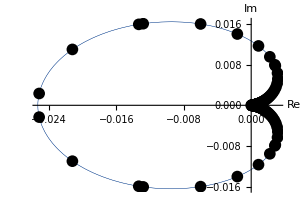

```mathematica
show1=Show[plot7, plot5]
```

As shown in show2, the singularity is a large relative distance from the rest of the function trace.

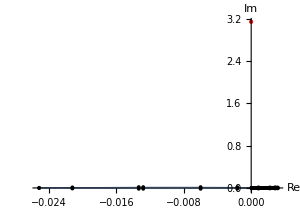

```mathematica
show2=Show[plot7, plot4]
```

The text does not list an answer for this problem, but I believe that R is defined by 0<|π ⅈ|<∞.

13.  1/(z^3(z- ⅈ)^2) , z_0=ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
fn[z_]=1/(z^3(z- ⅈ)^2)
```

1/(z^3 (-ⅈ+z)^2)

```mathematica
Series[fn[z],{z, ⅈ,4}]
```

ⅈ/(z-ⅈ)^2-3/(z-ⅈ)-6 ⅈ+10 (z-ⅈ)+15 ⅈ (z-ⅈ)^2-21 (z-ⅈ)^3-28 ⅈ (z-ⅈ)^4+O[z-ⅈ]^5

The green cell above matches the answer in the text.

```mathematica
FindSequenceFunction[{ⅈ,-3,-6 ⅈ,10,15 ⅈ,-21,-28 ⅈ},n]
```

1/2 ⅈ^n n (1+n)

```mathematica
Limit[Abs[(1/2 ⅈ^n n (1+n))/1(1/(1/2 ⅈ^(n+1) (n+2) (1+n)))],n->∞]
```

1

```mathematica
FindSequenceFunction[{-2,-1,0,1,2,3,4},n]
```

-3+n

```mathematica
1^(1/1)
```

1

As in problem 1 and for the same reason, I will express the radius of convergence as 0<|z - 1|<1, in agreement with the answer in the text.

15.  Cos[z]/(z- π)^2, z_0=π

```mathematica
Clear["Global`*"]
```

```mathematica
fo[z_]=Cos[z]/(z- π)^2
```

Cos[z]/(-π+z)^2

```mathematica
Series[fo[z],{z, π,8}]
```

-1/(z-π)^2+1/2-1/24 (z-π)^2+1/720 (z-π)^4-(z-π)^6/40320+(z-π)^8/3628800+O[z-π]^9

The green cell matches the answer in the text.

```mathematica
FindSequenceFunction[{-1,1/2,-1/24,1/720,-1/40320,1/3628800},n]
```

((-1)^n 4^(1-n))/(Pochhammer[1/2,-1+n] Pochhammer[1,-1+n])

```mathematica
FullSimplify[%]
```

(-1)^n/Gamma[-1+2 n]

```mathematica
Limit[Abs[(-1)^n/Gamma[-1+2 n](Gamma[-1+2( n+1)]/(-1)^(n+1))],n->∞]
```

∞

```mathematica
FindSequenceFunction[{-2,0,2,4,6,8},n]
```

2 (-2+n)

```mathematica
∞^(1/2)
```

∞

As in problem 1 and for the same reason, I will express the radius of convergence as 0<|z - π|<∞, in agreement with the answer in the text.

19 - 25 Taylor and Laurent series
Find all Taylor and Laurent series with center z_0. Determine the precise regions of convergence.

19.  1/(1- z^2) , z_0=0

```mathematica
Clear["Global`*"]
```

```mathematica
fp[z_]=1/(1- z^2)
```

1/(1-z^2)

```mathematica
Series[fp[z],{z, 0,14}]
```

1+z^2+z^4+z^6+z^8+z^10+z^12+z^14+O[z]^15

The green cell matches the answer in the text.

```mathematica
FindSequenceFunction[{1,1,1,1,1,1,1},n]
```

1

```mathematica
Limit[Abs[1/1],n->∞]
```

1

```mathematica
FindSequenceFunction[{0,2,4,6,8,10},n]
```

2 (-1+n)

```mathematica
1^(1/2)
```

1

```mathematica
Abs[z]<1
```

Okay, caught me napping. I see from the answer that I am back to the same examples 3 and 4 that I worked with in problem 5. If Abs[z]>1 then I can look at

```mathematica
1/(1-z^2)==-1/(z^2(1-z^-2));
```

and taking the cue from example 4,

```mathematica
-Sum[z^(-2n -2),{n,0,∞}]      (*  Abs[z]>1  *)
```

-1/(-1+z^2)

The green cell matches the answer in the text.

21. Sin[z]/(z+π/2) , z_0=-π/2

```mathematica
Clear["Global`*"]
```

```mathematica
fq[z_]=Sin[z]/(z+π/2)
```

Sin[z]/(π/2+z)

```mathematica
Series[fq[z],{z, -π/2,14}]
```

-1/(z+π/2)+1/2 (z+π/2)-1/24 (z+π/2)^3+1/720 (z+π/2)^5-(z+π/2)^7/40320+(z+π/2)^9/3628800-(z+π/2)^11/479001600+(z+π/2)^13/87178291200+O[z+π/2]^15

```mathematica
FindSequenceFunction[{-1,1/2,-1/24,1/720,-1/40320,1/3628800,-1/479001600},n]
```

((-1)^n 4^(1-n))/(Pochhammer[1/2,-1+n] Pochhammer[1,-1+n])

```mathematica
FullSimplify[%]
```

(-1)^n/Gamma[-1+2 n]

```mathematica
Limit[Abs[(-1)^n/Gamma[-1+2 n](Gamma[-1+2( n+1)]/(-1)^(n+1))],n->∞]
```

∞

```mathematica
FindSequenceFunction[{-1,1,3,5,7,9,11},n]
```

-3+2 n

```mathematica
∞^(1/2)
```

∞

The only modification to this result is the allowance for the singularity, so 0<|z+π/2|<∞

23. z^8/(1- z^4) , z_0=0

```mathematica
Clear["Global`*"]
```

```mathematica
fr[z_]=z^8/(1- z^4)
```

z^8/(1-z^4)

```mathematica
Series[fr[z],{z, 0,32}]
```

z^8+z^12+z^16+z^20+z^24+z^28+z^32+O[z]^33

The green cell matches the answer in the text.

```mathematica
FindSequenceFunction[{1,1,1,1,1,1,1},n]
```

1

```mathematica
Limit[Abs[1/1],n->∞]
```

1

The only modification to this result is the allowance for the singularity, so |z|<1

I note that this problem function is like problem 5 and problem 19, in that the radius is split into two parts. Another part with Abs[z]>1 also exists. In this case

```mathematica
z^8/(1-z^4)==z^-8/z^-8 z^8/(1-z^4)==1/(z^-8-z^-4)==1/(z^-8(1-z^4));
```

According to the website referred to earlier, expanding a series around Infinity causes Mathematica to automatically expand in terms of 1/z. A comment on the website indicates that this is sometimes performed to examine the outer region of an annular domain.

```mathematica
fs[z_]=Series[1/(z^-8(1-z^4)),{z,∞,20}]
```

-z^4-1-(1/z)^4-(1/z)^8-(1/z)^12-(1/z)^16-(1/z)^20+O[1/z]^21

and matching this recast is

```mathematica
Sum[z^(4n +8),{n,0,∞}]    (*  Abs[z]>1  *)
```

z^8/(1-z^4)

Heading towards finding a radius,

```mathematica
FindSequenceFunction[{-1,-1,-1,-1,-1,-1,-1},n]
```

-1

```mathematica
Limit[Abs[-1/-1],n->∞]
```

1

```mathematica
FindSequenceFunction[{4,0,-4,-8,-12,-16,-20},n]
```

-4 (-2+n)

```mathematica
1^(-1/4)
```

1

For this second version of the analysis, the radius is |z| > 1.

25.  (z^3-2 ⅈ z^2)/(z- ⅈ)^2 , z_0=ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
ft[z_]=(z^3-2 ⅈ z^2)/(z- ⅈ)^2
```

(-2 ⅈ z^2+z^3)/(-ⅈ+z)^2

```mathematica
Series[ft[z],{z, ⅈ,12}]
```

ⅈ/(z-ⅈ)^2+1/(z-ⅈ)+ⅈ+(z-ⅈ)+O[z-ⅈ]^13

I need to drop the higher-order remainder term. There is no remainder term, because the series contains only three terms. It is not infinite.

```mathematica
Normal[ⅈ/(z-ⅈ)^2+1/(z-ⅈ)+ⅈ+(z-ⅈ)+O[z-ⅈ]^13]
```

z+ⅈ/(-ⅈ+z)^2+1/(-ⅈ+z)

The above green cell matches the answer in the text, in content. Mathematica made a slight simplification, which I do not know how to avoid.

```mathematica
Limit[(ⅈ/(z-ⅈ)^2+1/(z-ⅈ)+ⅈ+(z-ⅈ)),Abs[z-ⅈ]->0]
```

(z^2 (-2 ⅈ+z))/(-ⅈ+z)^2

```mathematica
Limit[(ⅈ/(z-ⅈ)^2+1/(z-ⅈ)+ⅈ+(z-ⅈ)),Abs[z-ⅈ]->∞]
```

(z^2 (-2 ⅈ+z))/(-ⅈ+z)^2

I can invent a function and make a table.

```mathematica
chk[z_]=(z^2 (-2 ⅈ+z))/(-ⅈ+z)^2
```

(z^2 (-2 ⅈ+z))/(-ⅈ+z)^2

```mathematica
TableForm[N[Table[{z,chk[z]},{z,{-100,-5,-2,-1,-0.5,0,0.5,1,2,0.999( ⅈ),5,100}}]]]
```

-100. | -100.01+0.00019996 ⅈ
-5. | -5.17751+0.0739645 ⅈ
-2. | -2.24+0.32 ⅈ
-1. | -1.+0.5 ⅈ
-0.5 | -0.26+0.32 ⅈ
0. | 0.
0.5 | 0.26+0.32 ⅈ
1. | 1.+0.5 ⅈ
2. | 2.24+0.32 ⅈ
0.+0.999 ⅈ | 0.-998999. ⅈ
5. | 5.17751+0.0739645 ⅈ
100. | 100.01+0.00019996 ⅈ

For all points in the complex plane except the singularity, the expression generates a valid value, and all such locations belong within the radius of convergence.

```mathematica
chka[z_]=ComplexExpand[chk[z]]
```

(2 ⅈ z^2)/((1+z^2)^2)+(3 z^3)/((1+z^2)^2)+z^5/((1+z^2)^2)

```mathematica
plot1=ParametricPlot[{Re[chk[z]],Im[chk[z]]},{z,-100,100},ImageSize->300,AxesLabel->{"Re","Im"},PlotRange->{-1,1},AspectRatio->Automatic,GridLines->Automatic,PlotStyle->{Thickness[0.003]}];
```

```mathematica
rek=N[Table[{z,Im[chk[z]]},{z,{-100,-5,-2,-1,-0.5,0,0.5,1,2,5,100}}]]
```

{{-100.,0.00019996},{-5.,0.0739645},{-2.,0.32},{-1.,0.5},{-0.5,0.32},{0.,0.},{0.5,0.32},{1.,0.5},{2.,0.32},{5.,0.0739645},{100.,0.00019996}}

```mathematica
reki={{0,1}}
```

{{0,1}}

```mathematica
plot6=ParametricPlot[{Re[chk[z]],Im[chk[z]]},{z,-100,100},ImageSize->700,AspectRatio->0.2,PlotRange->All,PlotStyle->{Thickness[0.001]},AxesLabel->{"Re","Im"}];
```

```mathematica
plot4=ListPlot[{Re[#],Im[#]}& /@ rek,PlotRange->All,PlotStyle->Black,PlotMarkers->{•,12}];
```

```mathematica
plot5=ListPlot[{Re[#],Re[#]}& /@ reki,PlotRange->All,PlotStyle->Orange,PlotMarkers->{•,18}];
```

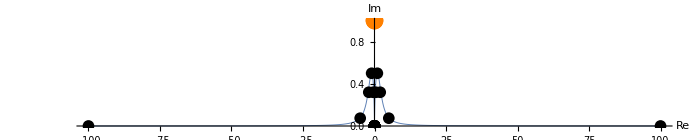

```mathematica
Show[plot6,plot4,plot5]
```

The orange dot shows the position of the singularity in relation to the function trace.

The text does not list an answer for this problem, but I believe that R is defined by 0<|0 + ⅈ|<∞.